## General Homogeneous Solution

```mathematica
xsol= DSolve[x''''[z]+A*x''[z]+B*x[z]==0,x[z],z];

xsol//.{
Sqrt[A-Sqrt[A^2-4 B]]/Sqrt[2]->λ1,
Sqrt[A+Sqrt[A^2-4 B]]/Sqrt[2]->λ2}

x[z_]:=E^(z λ1) l1+E^(-z λ1) l2+E^(z λ2) l3+E^(-z λ2) l4;
x[z]
```

{{x[z]→ⅇ^((√(-A-√(A^2-4 B)) z)/(√2)) C[1]+ⅇ^(-(√(-A-√(A^2-4 B)) z)/(√2)) C[2]+ⅇ^((√(-A+√(A^2-4 B)) z)/(√2)) C[3]+ⅇ^(-(√(-A+√(A^2-4 B)) z)/(√2)) C[4]}}

ⅇ^(z λ1) l1+ⅇ^(-z λ1) l2+ⅇ^(z λ2) l3+ⅇ^(-z λ2) l4

```mathematica
ysol=C0*D[x[z],{z,3}]-D0*D[x[z],z]//FullSimplify
```

ⅇ^(-z λ1) (ⅇ^(2 z λ1) l1-l2) λ1 (-D0+C0 λ1^2)+ⅇ^(-z λ2) l4 λ2 (D0-C0 λ2^2)+ⅇ^(z λ2) l3 λ2 (-D0+C0 λ2^2)

## Particular Solution

```mathematica
Amat={
{1,1,1,1,0,0,0,0},

{γ1,-γ1,γ2,-γ2,0,0,0,0},

{0,0,0,0,Exp[λ1*d],Exp[-λ1*d],Exp[λ2*d],Exp[-λ2*d]},

{0,0,0,0,γ1*Exp[λ1*d],-γ1*Exp[-λ1*d],γ2*Exp[λ2*d],-γ2*Exp[-λ2*d]},

{Exp[λ1*z],Exp[-λ1*z], Exp[λ2*z],Exp[-λ2*z],-Exp[λ1*z],-Exp[-λ1*z], -Exp[λ2*z],-Exp[-λ2*z]},

{γ1*Exp[λ1*z],-γ1*Exp[-λ1*z],γ2*Exp[λ2*z],-γ2*Exp[-λ2*z],-γ1*Exp[λ1*z],γ1*Exp[-λ1*z], -γ2*Exp[λ2*z],γ2*Exp[-λ2*z]},

{λ1*Exp[λ1*z],-λ1*Exp[-λ1*z],λ2*Exp[λ2*z],-λ2*Exp[-λ2*z],-λ1*Exp[λ1*z],λ1*Exp[-λ1*z], -λ2*Exp[λ2*z],λ2*Exp[-λ2*z]},

{γ1*λ1*Exp[λ1*z],γ1*λ1*Exp[-λ1*z],γ2*λ2*Exp[λ2*z],γ2*λ2*Exp[-λ2*z],-γ1*λ1*Exp[λ1*z],-γ1*λ1*Exp[-λ1*z], -γ2*λ2*Exp[λ2*z],-γ2*λ2*Exp[-λ2*z]}
}//.{z->Z};

Amat//MatrixForm
```

(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
γ1 | -γ1 | γ2 | -γ2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(d λ1) | ⅇ^(-d λ1) | ⅇ^(d λ2) | ⅇ^(-d λ2)
0 | 0 | 0 | 0 | ⅇ^(d λ1) γ1 | -ⅇ^(-d λ1) γ1 | ⅇ^(d λ2) γ2 | -ⅇ^(-d λ2) γ2
ⅇ^(Z λ1) | ⅇ^(-Z λ1) | ⅇ^(Z λ2) | ⅇ^(-Z λ2) | -ⅇ^(Z λ1) | -ⅇ^(-Z λ1) | -ⅇ^(Z λ2) | -ⅇ^(-Z λ2)
ⅇ^(Z λ1) γ1 | -ⅇ^(-Z λ1) γ1 | ⅇ^(Z λ2) γ2 | -ⅇ^(-Z λ2) γ2 | -ⅇ^(Z λ1) γ1 | ⅇ^(-Z λ1) γ1 | -ⅇ^(Z λ2) γ2 | ⅇ^(-Z λ2) γ2
ⅇ^(Z λ1) λ1 | -ⅇ^(-Z λ1) λ1 | ⅇ^(Z λ2) λ2 | -ⅇ^(-Z λ2) λ2 | -ⅇ^(Z λ1) λ1 | ⅇ^(-Z λ1) λ1 | -ⅇ^(Z λ2) λ2 | ⅇ^(-Z λ2) λ2
ⅇ^(Z λ1) γ1 λ1 | ⅇ^(-Z λ1) γ1 λ1 | ⅇ^(Z λ2) γ2 λ2 | ⅇ^(-Z λ2) γ2 λ2 | -ⅇ^(Z λ1) γ1 λ1 | -ⅇ^(-Z λ1) γ1 λ1 | -ⅇ^(Z λ2) γ2 λ2 | -ⅇ^(-Z λ2) γ2 λ2)

```mathematica
Ainv=Amat//Inverse;
y13={{0},{0},{0},{0},{0},{0},{1},{0}};
y24={{0},{0},{0},{0},{0},{0},{0},{1}};

x13=Ainv.y13;
x24=Ainv.y24;
```

```mathematica
{l1,l2,l3,l4,r1,r2,r3,r4}=Flatten[x13];
```

## Plots

```mathematica
rules={
Δ->A0^2-4B0,
λ1->1/Sqrt[2]*Sqrt[A0-Δ],
λ2->1/Sqrt[2]*Sqrt[A0+Δ],
γ1->λ1(λ1^2 C0-D0),
γ2->λ2(λ2^2 C0-D0),

A0->a0+c0+b0*d0,B0->a0*c0,
C0->1/(b0*c0),D0->(a0+b0*d0)/(b0*c0),

a0->-E0p/(B1-D1),
b0->I p A1/(B1-D1), 
c0->E0m/(B1+D1),
d0->-I p A1/(B1+D1),

E0p->ϵ0+μ0+p Λ-ω,E0m->ϵ0-μ0+p Λ-ω,

ϵ0->-0.0068,μ0->0.28,Λ->0.010,
A1->2.2,B1->10,D1->1.3
};


L1[ℏω_,x_,X_,spin_,thickness_]:=Evaluate[l1//.rules/.{ω->ℏω,z->x,Z->X,p->spin,d->thickness}]
L2[ℏω_,x_,X_,spin_,thickness_]:=Evaluate[l2//.rules/.{ω->ℏω,z->x,Z->X,p->spin,d->thickness}]
L3[ℏω_,x_,X_,spin_,thickness_]:=Evaluate[l3//.rules/.{ω->ℏω,z->x,Z->X,p->spin,d->thickness}]
L4[ℏω_,x_,X_,spin_,thickness_]:=Evaluate[l4//.rules/.{ω->ℏω,z->x,Z->X,p->spin,d->thickness}]

R1[ℏω_,x_,X_,spin_,thickness_]:=Evaluate[r1//.rules/.{ω->ℏω,z->x,Z->X,p->spin,d->thickness}]
R2[ℏω_,x_,X_,spin_,thickness_]:=Evaluate[r2//.rules/.{ω->ℏω,z->x,Z->X,p->spin,d->thickness}]
R3[ℏω_,x_,X_,spin_,thickness_]:=Evaluate[r3//.rules/.{ω->ℏω,z->x,Z->X,p->spin,d->thickness}]
R4[ℏω_,x_,X_,spin_,thickness_]:=Evaluate[r4//.rules/.{ω->ℏω,z->x,Z->X,p->spin,d->thickness}]
```

#### Left Coefficients

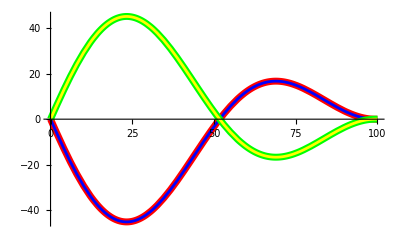

```mathematica
Plot[
{L1[0.002,z,z,1,100]//Re,
L2[0.002,z,z,1,100]//Re,
L3[0.002,z,z,1,100]//Re,
L4[0.002,z,z,1,100]//Re},

{z,0,100},

PlotStyle->{
{AbsoluteThickness[5],Red}, 
{AbsoluteThickness[2],Blue},
{AbsoluteThickness[5],Green},
{AbsoluteThickness[2],Yellow}}
]
```

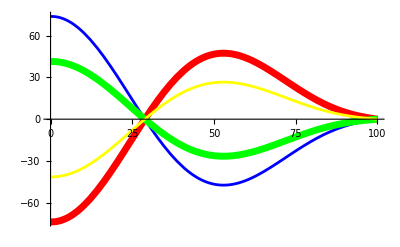

```mathematica
Plot[
{L1[0.001,z,z,1,100]//Im,
L2[0.001,z,z,1,100]//Im,
L3[0.001,z,z,1,100]//Im,
L4[0.001,z,z,1,100]//Im},

{z,0,100},

PlotStyle->{
{AbsoluteThickness[5],Red}, 
{AbsoluteThickness[2],Blue},
{AbsoluteThickness[5],Green},
{AbsoluteThickness[2],Yellow}}
]
```

#### Right Coefficients

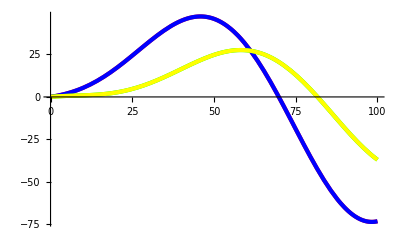

```mathematica
Plot[
{R1[0.001,z,z,1,100]//Re,
R2[0.001,z,z,1,100]//Re,
R3[0.001,z,z,1,100]//Re,
R4[0.001,z,z,1,100]//Re},

{z,0,100},

PlotStyle->{
{AbsoluteThickness[3],Red}, 
{AbsoluteThickness[3],Blue},
{AbsoluteThickness[3],Green},
{AbsoluteThickness[3],Yellow}}
]
```

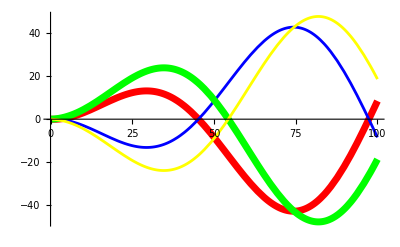

```mathematica
Plot[
{R1[0.001,z,z,1,100]//Im,
R2[0.001,z,z,1,100]//Im,
R3[0.001,z,z,1,100]//Im,
R4[0.001,z,z,1,100]//Im},

{z,0,100},

PlotStyle->{
{AbsoluteThickness[5],Red}, 
{AbsoluteThickness[2],Blue},
{AbsoluteThickness[5],Green},
{AbsoluteThickness[2],Yellow}}
]
```

```mathematica
L1[-0.001,5,5,1,100]+L2[-0.001,5,5,1,100]
L1[-0.001,5,5,1,100]-L2[-0.001,5,5,1,100]

L3[-0.001,5,5,1,100]+L4[-0.001,5,5,1,100]
L3[-0.001,5,5,1,100]-L4[-0.001,5,5,1,100]
```

-30.798+0. ⅈ

3.55271×10^-14-139.81 ⅈ

30.798+1.42109×10^-14 ⅈ

-1.77636×10^-14+78.6519 ⅈ